```mathematica
(*
  Need an approximation for alpha such that 
        alpha(1-3R0^2) > nq 
		alpha(3R0^2-1) < nq
Set alpha = A nq
		A(3R0^2-1) < 1
if A > 0 and B^2 = (1/A+1)/3
		R0^2 - B < 0
		(R0 - B)(R0 + B) < 0 
			-B < R0 < B

*)
FullSimplify[With[{alpha=2*(eta q)/(1-3 R0^2)}, -eta k^2+1/2 (alpha q-eta q^2-3 alpha q R0^2+ √(4 alpha^2 k^2-16 alpha eta k^2 q+alpha^2 q^2+16 eta^2 k^2 q^2-2 alpha eta q^3+eta^2 q^4-8 alpha^2 k^2 R0^2+16 alpha eta k^2 q R0^2-6 alpha^2 q^2 R0^2+6 alpha eta q^3 R0^2+4 alpha^2 k^2 R0^4+9 alpha^2 q^2 R0^4))]]
```

1/2 (eta (-2 k^2+q^2)+√((eta^2 q^2 (64 k^2 R0^4+q^2 (1-3 R0^2)^2))/((1-3 R0^2)^2)))

```mathematica
Simplify[1/2 (eta (-2 k^2+q^2)+(eta q 8 k R0^2)/Modulus[(1-3 R0^2)]+eta q^2)]
```

eta (-k^2+q^2+(4 k q R0^2)/Modulus[1-3 R0^2])

```mathematica
Solve[-k^2+q^2+(4 k q R0^2)/Modulus[1-3 R0^2]==0,k]
```

{{k→1/2 (-√(4 q^2+(16 q^2 R0^4)/(Modulus[1-3 R0^2]^2))+(4 q R0^2)/Modulus[1-3 R0^2])},{k→1/2 (√(4 q^2+(16 q^2 R0^4)/(Modulus[1-3 R0^2]^2))+(4 q R0^2)/Modulus[1-3 R0^2])}}

```mathematica
Simplify[1/2 (2q √(1+(4 R0^4)/(Modulus[1-3 R0^2]^2))+(4 q R0^2)/Modulus[1-3 R0^2])]
```

```mathematica
(√((1-3 R0^2)^2+4 R0^4)+2 R0^2)/Modulus[1-3 R0^2]
```

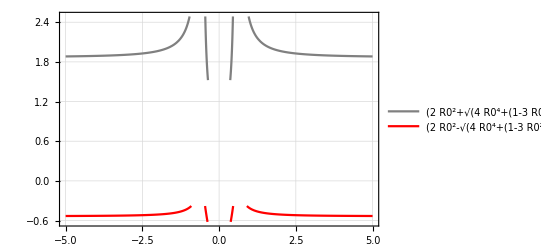

```mathematica
p1=Plot[(2 R0^2+√(4 R0^4+(1-3 R0^2)^2))/Abs[1-3 R0^2],{R0,-5,5},PlotTheme->"Detailed", PlotStyle->Gray];
p2=Plot[(2 R0^2-√(4 R0^4+(1-3 R0^2)^2))/Abs[1-3 R0^2],{R0,-5,5},PlotTheme->"Detailed", PlotStyle->Red];
Show[{p1,p2}, PlotRange->All, AxesLabel->{R_0}]
```

```mathematica
Limit[(2 R0^2+√(4 R0^4+(1-3 R0^2)^2))/Abs[1-3 R0^2],R0 -> Infinity]
```

1/3 (2+√13)

```mathematica
N[1/3 (2-√13)]
```

-0.535184